# Misner Space

Spacetime discussed in Section 2.7, p 81, Carroll
ds^2=t/(√(1+t^2))dt^2-2/(√(1+t^2))  dt dx -t/(√(1+t^2)) dx^2
0<x<1, -∞<t<+∞

-Graphics-

## Initialization

```mathematica
Needs["xAct`xCoba`"]
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2018, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.3, {2018,2,28}

CopyRight (C) 2002-2018, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.4, {2018,2,28}

CopyRight (C) 2005-2018, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
(*$PrePrint=ScreenDollarIndices;
$DefInfoQ=False;
$UndefInfoQ=False;*)
```

```mathematica
DefManifold[M,2,{λ,μ,ν,ρ,σ,α,β,γ,δ}];
dimM = DimOfManifold[M];dimM1 = dimM-1;
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

Here is the definition of the coordinate system, and the metric:
Simply define the list coords = {....} and the matrix gmatrix

```mathematica
coords = {t[],x[]};
(*DefConstantSymbol[mass,PrintAs->"M"];*)
DefScalarFunction[ascale,PrintAs->"a"]; (*Use as e.g. ascale[t[],r[]] for a function of (t,r)*)
gmatrix = {
{t[]/(√(1+t[]^2)),   -1/(√(1+t[]^2))},
{  -1/(√(1+t[]^2)),  (-t[])/(√(1+t[]^2))}
};
DefChart[ch,M,{0,1},coords,ChartColor->Blue];
g=CTensor[gmatrix,{-ch,-ch}];
SetCMetric[g,ch,SignatureOfMetric-> {1,1,0}];
CD = CovDOfMetric[g];
$Assumptions = 0<x[]<1 && t∈Reals;
```

** DefScalarFunction: Defining scalar function ascale.

** DefChart: Defining chart ch.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar x[].

** DefMapping: Defining mapping ch.

** DefMapping: Defining inverse mapping ich.

** DefTensor: Defining mapping differential tensor dich[-a,ichα].

** DefTensor: Defining mapping differential tensor dch[-α,cha].

** DefBasis: Defining basis ch. Coordinated basis.

** DefCovD: Defining parallel derivative PDch[-α].

** DefTensor: Defining vanishing torsion tensor TorsionPDch[α,-β,-γ].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch[α,-β,-γ].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch[-α,-β,-γ,δ].

** DefTensor: Defining vanishing Ricci tensor RicciPDch[-α,-β].

** DefTensor: Defining antisymmetric +1 density etaUpch[α,β].

** DefTensor: Defining antisymmetric -1 density etaDownch[-α,-β].

```mathematica
Print[
"g_μν= ",ComponentArray[g[{-μ,-ch},{-ν,-ch}]]//MatrixForm,"    ,       ",
"g^μν= ",ComponentArray[g[{  μ,   ch},{   ν,  ch}]]//MatrixForm,"\n",
"g  =", Determinant[g,ch][]," = ",Det[ComponentArray[g[{-μ,-ch},{-ν,-ch}]]]//Simplify
]
```

g_μν= (t/(√(1+t^2)) | -1/(√(1+t^2))
-1/(√(1+t^2)) | -t/(√(1+t^2)))    ,       g^μν= (t/(√(1+t^2)) | -1/(√(1+t^2))
-1/(√(1+t^2)) | -t/(√(1+t^2)))
g  =OverTilde[OverTilde[-1]] = -1

## Affine Connection

Print nonzero components:
(Γ^λ)_μν=1/2 g^λσ(∂_μ g_σν+∂_ν g_σμ-∂_σ g_μν)
The components of the Christoffel symbols are collected  by the ComponentArray[expr] function.

```mathematica
list =ComponentArray[Christoffel[CD,PDch][{α,ch},{-β,-ch},{-γ,-ch}]];
list = Table[
If[
UnsameQ[list[[i,j,k]],0],{Subscript[Superscript["Γ",i-1],j-1,k-1],list[[i,j,k]]}
],
{i,1,Length[list]},{j,1,Length[list]},{k,1,j}
];
Partition[DeleteCases[Flatten[list],Null],2]//TableForm
```

(Γ^0)_(0,0) | -t/(2 (1+t^2)^2)
(Γ^0)_(1,0) | 1/(2 (1+t^2)^2)
(Γ^0)_(1,1) | t/(2 (1+t^2)^2)
(Γ^1)_(0,0) | -(1+2 t^2)/(2 (1+t^2)^2)
(Γ^1)_(1,0) | t/(2 (1+t^2)^2)
(Γ^1)_(1,1) | -1/(2 (1+t^2)^2)

## Curvature

Print nonzero components of Riemann: (R^μ)_νρσ
(R^λ)_ρμν = ∂_μ (Γ^λ)_νρ-∂_ν (Γ^λ)_μρ + (Γ^λ)_μσ (Γ^σ)_νρ - (Γ^λ)_νσ (Γ^σ)_μρ  (Carroll+Hartle’s convention)
xCoba has Wald’s convention, which for a Levi-Civita Connection gives the same reult after some index raising/lowering.

The components of the Riemann tensor are collected by the ComponentArray[expr] function.

```mathematica
list=ComponentArray[Riemann[CD][{α,ch},{-β,-ch},{-γ,-ch},{-δ,-ch}]];
list = Table[
If[
UnsameQ[list[[i,j,k,l]],0],{Subscript[Superscript["R",i-1],j-1,k-1,l-1]
,list[[i,j,k,l]]}
],
{i,1,Length[list]},{j,1,Length[list]},{k,1,Length[list]},{l,1,k-1}
];
Partition[DeleteCases[Flatten[list],Null],2]//TableForm
```

(R^0)_(0,1,0) | (3 t)/(2 (1+t^2)^3)
(R^0)_(1,1,0) | (3 t^2)/(2 (1+t^2)^3)
(R^1)_(0,1,0) | (3 t^2)/(2 (1+t^2)^3)
(R^1)_(1,1,0) | -(3 t)/(2 (1+t^2)^3)

The Riemann tensor with all lower indices: R_μνρσ

```mathematica
list=ComponentArray[Riemann[CD][{-α,-ch},{-β,-ch},{-γ,-ch},{-δ,-ch}]];
list = Table[
If[
UnsameQ[list[[i,j,k,l]],0],{Subscript["R",i-1,j-1,k-1,l-1]
,list[[i,j,k,l]]}
],
{i,1,Length[list]},{j,1,i-1},{k,1,Length[list]},{l,1,k-1}
];
Partition[DeleteCases[Flatten[list],Null],2]//TableForm
```

R_(1,0,1,0) | -(3 t)/(2 (1+t^2)^(5/2))

The Riemann tensor with all upper indices: R^μνρσ

```mathematica
list=ComponentArray[Riemann[CD][{α,ch},{β,ch},{γ,ch},{δ,ch}]];
list = Table[
If[
UnsameQ[list[[i,j,k,l]],0],{Superscript[Superscript[Superscript[Superscript["R",i-1],j-1],k-1],l-1]
,list[[i,j,k,l]]}
],
{i,1,Length[list]},{j,1,i-1},{k,1,Length[list]},{l,1,k-1}
];
Partition[DeleteCases[Flatten[list],Null],2]//TableForm
```

(((R^1)^0)^1)^0 | -(3 t)/(2 (1+t^2)^(5/2))

The Ricci tensor: R_μν

```mathematica
list=ComponentArray[Ricci[CD][{-α,-ch},{-β,-ch}]];
list = Table[
If[
UnsameQ[list[[i,j]],0],{Subscript["R",i-1,j-1]
,list[[i,j]]}
],
{i,1,Length[list]},{j,1,i}
];
Partition[DeleteCases[Flatten[list],Null],2]//TableForm
```

R_(0,0) | (3 t^2)/(2 (1+t^2)^3)
R_(1,0) | -(3 t)/(2 (1+t^2)^3)
R_(1,1) | -(3 t^2)/(2 (1+t^2)^3)

Ricci scalar:

```mathematica
Print["R = ",RicciScalar[CD][]]
```

R = (3 t)/((1+t^2)^(5/2))

R^2 scalar

```mathematica
Print["R^2 = ",Kretschmann[CD][]]
```

R^2 = (9 t^2)/((1+t^2)^5)

## Geodesic Equations

```mathematica
DefTensor[u[μ],M];
```

** DefTensor: Defining tensor u[μ].

The geodesic equations are:
du^μ/dτ+(Γ^μ)_(⋁ρ)u^ν u^ρ=0
geqs is a list with the second term geqs[μ+1]= (Γ^μ)_(⋁ρ)u^ν u^ρ for each μ=0,..,d-1.
(careful, in the expressions below, when e.g.  u^(3^2)=(u^3)^2, the squared terms don’t appear nicely)

```mathematica
geqs=ComponentArray[Christoffel[CD,PDch][{μ,ch},{-ν,-ch},{-ρ,-ch}] u[{ν,ch}]u[{ρ,ch}]]//ContractBasis//Simplify;
For[i=1,i<= Length[geqs],i++,Print["d/dτ",u[{i-1,ch}],"+(",geqs[[i]],")=0"]]
```

d/dτu | 0
 +((-t (u | 0)^2+2 u | 0
  u | 1
 +t (u | 1)^2)/(2 (1+t^2)^2))=0

d/dτu | 1
 +(-((1+2 t^2) (u | 0)^2-2 t u | 0
  u | 1
 +(u | 1)^2)/(2 (1+t^2)^2))=0

```mathematica
DefScalarFunction[  dx0  ,PrintAs->"ṫ"];DefScalarFunction[  dx1  ,PrintAs->"ẋ"];
DefScalarFunction[ddx0  ,PrintAs->"ẗ"];DefScalarFunction[ddx1  ,PrintAs->"ẍ"];
u   = CTensor[{  dx0[] ,  dx1[]},{ch}];
du = CTensor[{ddx0[],ddx1[]},{ch}];
{u,du}
```

** DefScalarFunction: Defining scalar function dx0.

** DefScalarFunction: Defining scalar function dx1.

** DefScalarFunction: Defining scalar function ddx0.

** DefScalarFunction: Defining scalar function ddx1.

{CTensor[{ṫ[],ẋ[]},{ch},0],CTensor[{ẗ[],ẍ[]},{ch},0]}

```mathematica
geqs=ComponentArray[Christoffel[CD,PDch][{μ,ch},{-ν,-ch},{-ρ,-ch}] u[{ν,ch}]u[{ρ,ch}]]//ContractBasis//Simplify;
For[i=1,i<= Length[geqs],i++,Print[du[{i-1,ch}],"+(",geqs[[i]],")=0"]]
```

ẗ[]+((2 ṫ[] ẋ[]-(ṫ[])^2 t+(ẋ[])^2 t)/(2 (1+t^2)^2))=0

ẍ[]+(-((ẋ[])^2-2 ṫ[] ẋ[] t+(ṫ[])^2 (1+2 t^2))/(2 (1+t^2)^2))=0

```mathematica
u[μ] u[-μ]//Simplify
```

(-2 ṫ[] ẋ[]+(ṫ[])^2 t-(ẋ[])^2 t)/(√(1+t^2))

```mathematica
Clear[tcp0,xcp0,xc0,tc0];
nullcon = Solve[((u[μ] u[-μ]//Simplify) /.{dx0[]-> tcp0,dx1[]-> xcp0, x[]-> xc0, t[]-> tc0}) ==0,tcp0]
```

{{tcp0→(xcp0-√(xcp0^2+tc0^2 xcp0^2))/tc0},{tcp0→(xcp0+√(xcp0^2+tc0^2 xcp0^2))/tc0}}

```mathematica
rhs = -(geqs /. {dx0[]-> tcp[τ],dx1[]-> xcp[τ], x[]-> xc[τ], t[]-> tc[τ]}/.{xcp[τ] -> xc'[τ],tcp[τ] -> tc'[τ]})
```

{-(-tc[τ] tc'[τ]^2+2 tc'[τ] xc'[τ]+tc[τ] xc'[τ]^2)/(2 (1+tc[τ]^2)^2),((1+2 tc[τ]^2) tc'[τ]^2-2 tc[τ] tc'[τ] xc'[τ]+xc'[τ]^2)/(2 (1+tc[τ]^2)^2)}

```mathematica
tcp0 = tcp0 /.nullcon
```

{(xcp0-√(xcp0^2+tc0^2 xcp0^2))/tc0,(xcp0+√(xcp0^2+tc0^2 xcp0^2))/tc0}

Notice that the horizontal lines are not part of the curve, they represent the jump to the other side of the strip.
I don’t know how to get rid of that (I tried Exclusions→”Discontinuities”, doesn’t work)

x_0= 0.5  t_0= -1.  (ẋ)_0= -0.9  (ṫ)_0= 2.17279

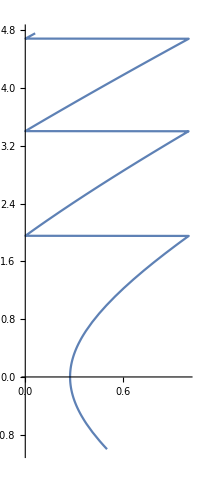
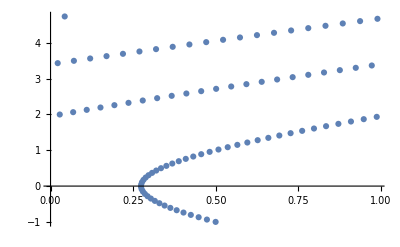
{-Graphics-,-Graphics3D-,-Graphics-}

```mathematica
Clear[tcp0,xcp0,xc0,tc0];
xcp0 = -0.9; τmax= 2.65;
xc0   = 0.5;tc0 = -1.0;
direction = 1; (* 1 or 2, the two roots in nullcon. The negative sign is backwards in time t *)
tcp0= tcp0 /.nullcon[[direction,1]];
Print["x_0= ",xc0,"  t_0= ",tc0,"  (ẋ)_0= ", xcp0,"  (ṫ)_0= ",tcp0];
dsol = NDSolve[{
tc''[τ] == rhs[[1]],
xc''[τ] == rhs[[2]],
tc'  [0] == tcp0,
xc'  [0] == xcp0,
tc     [0] == tc0,
xc     [0] == xc0
},{tc,xc},{τ,0,τmax}
];
{ParametricPlot[Evaluate[{Mod[xc[τ],1.0],tc[τ]}/.dsol],{τ,0,τmax},Exclusions->"Discontinuities"],
ParametricPlot3D[Evaluate[{Cos[2 π xc[τ]],Sin[2 π xc[τ]],tc[τ]}/.dsol],{τ,0,τmax}],
ListPlot[Table[Evaluate[{Mod[xc[τ],1.0],tc[τ]}/.dsol[[1]]],{τ,0,τmax,0.03}]]}
```

```mathematica
Clear[tcp0,xcp0,xc0,tc0];
xcp0 = 0.9; τmax= 2.7;
xc0   = 0.5;tc0 = -1.0;
direction = 1; (* 1 or 2, the two roots in nullcon. The negative sign is backwards in time t *)
tcp0= tcp0 /.nullcon[[direction,1]];
Print["x_0= ",xc0,"  t_0= ",tc0,"  (ẋ)_0= ", xcp0,"  (ṫ)_0= ",tcp0];
dsol = NDSolve[{
tc''[τ] == rhs[[1]],
xc''[τ] == rhs[[2]],
tc'  [0] == tcp0,
xc'  [0] == xcp0,
tc     [0] == tc0,
xc     [0] == xc0
},{tc,xc},{τ,0,τmax}
];
{
ParametricPlot[Evaluate[{Mod[xc[τ],1.0],tc[τ]}/.dsol],{τ,0,τmax},Exclusions->"Discontinuities"],
ParametricPlot3D[Evaluate[{Cos[2 π xc[τ]],Sin[2 π xc[τ]],tc[τ]}/.dsol],{τ,0,τmax}],
ListPlot[Table[Evaluate[{Mod[xc[τ],1.0],tc[τ]}/.dsol[[1]]],{τ,0,τmax,0.03}],PlotStyle->PointSize[0.01]]
}
```

x_0= 0.5  t_0= -1.  (ẋ)_0= 0.9  (ṫ)_0= 0.372792

NDSolve::ndsz: At τ == 2.68246, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {2.7} lies outside the range of data in the interpolating function. Extrapolation will be used.

{-Graphics-,-Graphics3D-,-Graphics-}

## Acknowledgements

This notebook has been programmed by Konstantinos Anagnostopoulos, Physics Department, National Technical University of Athens, Greece, while he was an instructor of the 4th year undergraduate course "General Relativity and Cosmology". It was created for fun, but it may turn out to be useful to everyone studying the General Theory of Relativity for the first time.
Email: konstant@mail.ntua.gr
Web:    http://physics.ntua.gr/konstant 
It is offered under a GPL/CC BY 4.0 license (in that order, depending on whether they apply on the programming part or the text part of the notebook).